This first part is directly from the Help Menu

Specify a Schrödinger operator with parameter h and potential V:

```mathematica
V[x_]:=1/2 x^2
ℒ=-1/2 u''[x]+V[x]*u[x];
```

Find the 10 smallest eigenvalues and eigenfunctions on a refined mesh:

```mathematica
{vals,funs}=NDEigensystem[ℒ,u[x],{x,-10,10},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.05}}}}];
```

```mathematica
vals
```

{0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.50001,9.50001}

Visualize the eigenfunctions scaled by h and offset by the respective eigenvalue:

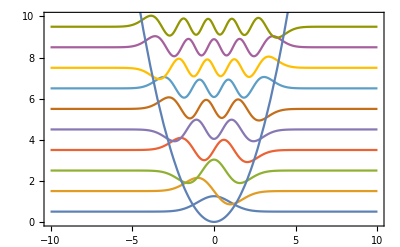

```mathematica
Show[Plot[Evaluate[funs+vals],{x,-10,10}],
Plot[V[x],{x,-10,10}],PlotRange->{{-10,10},{0,10}},Axes->False, Frame->True, FrameStyle->Large]
```

One can specify a particular log-derivative at one boundary by adding the NeumannValue.  Since the BP boundary condition is  -1/a=(1/u ⅆu/ⅆx)_(x→0) we have for n=-x that the “Neumann value” is (+1)/a u(0),

```mathematica
V[x_]:=1/2 x^2;ascat=1;
ℒ=-1/2 u''[x]+V[x]*u[x]+NeumannValue[1/ascat u[x],x==0];
```

Find the 10 smallest eigenvalues and eigenfunctions on a refined mesh:

```mathematica
{vals,funs}=NDEigensystem[ℒ,u[x],{x,0,10},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.05}}}}];
```

```mathematica
vals
```

{1.0839,2.93709,4.8623,6.8157,8.78325,10.759,12.7401,14.7248,16.712,18.7012}

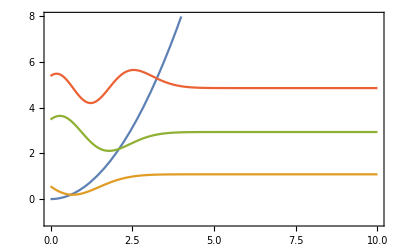

```mathematica
Plot[{V[x],funs[[1]]+vals[[1]],funs[[2]]+vals[[2]],funs[[3]]+vals[[3]]},{x,0,10.},PlotRange->{-1,8},Frame->True,Axes->False]
```

This looks good.  Positive a means an attractive potential in 1D and results in a dip in the wavefunction as x→0, as well as a lower energy.  a→0 means infinitely strong interactions, and a→±∞ means weak interactions.

```mathematica
ascat=10^10;ℒ=-1/2 u''[x]+V[x]*u[x]+NeumannValue[1/ascat u[x],x==0];
```

Find the 10 smallest eigenvalues and eigenfunctions on a refined mesh:

```mathematica
{vals,funs}=NDEigensystem[ℒ,u[x],{x,0,10},10,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.05}}}}];
```

```mathematica
vals
```

{0.5,2.5,4.5,6.5,8.50001,10.5,12.5,14.5,16.5,18.5001}

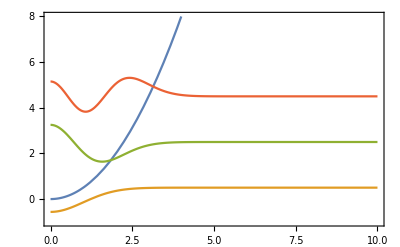

```mathematica
Plot[{V[x],funs[[1]]+vals[[1]],funs[[2]]+vals[[2]],funs[[3]]+vals[[3]]},{x,0,10.},PlotRange->{-1,8},Frame->True,Axes->False]
```

Let’s see what the errors in the harmonic oscillator solutions are like as a function of step size.  I’ll define the following module to calculate the errors in the first 4 states:

```mathematica
TestNDEigErrors[eps_,xmax_]:=
Module[{vals,funs},{vals,funs}=NDEigensystem[{-1/2 Laplacian[u[x],{x}]+1/2 x^2 u[x]},u,{x,-xmax,xmax},4,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->eps}}}}];
err=Abs[vals - {0.5,1.5,2.5,3.5}]
]
```

```mathematica
errs=TestNDEigErrors[.01,8π];nmax=Length[errs];
```

```mathematica
MeshSize=Table[eps,{eps,0.001,0.5,0.01}];neps=Length[MeshSize];
```

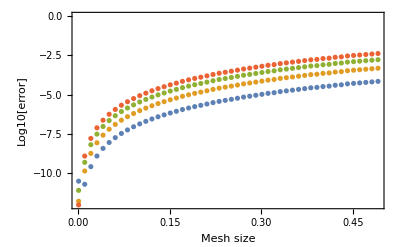

```mathematica
ListPlot[Table[{MeshSize[[n]],Log10[TestNDEigErrors[MeshSize[[n]],4π][[i]]]},{i,1,nmax},{n,1,neps}],Frame->True,FrameLabel->{"Mesh size","Log10[error]"}]
```

## Zero-range boundary conditions for the infinite square well

Let’s see if we can get the zero-range boundary condition using the “Robin boundary condition” imposed with the NeumannValue function.

```mathematica
{vals,funs}=NDEigensystem[{-Laplacian[u[x],{x}]+Piecewise[{{10000,x>10},{0,x<10}}]u[x]+NeumannValue[-1u[x],x==0]},u,{x,0,20},5,Method->{"FEAST"}]
```

{{0.120816,0.474283,-0.998742,1.0462,1.83043},{InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>]}}

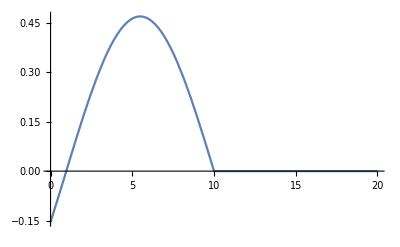

```mathematica
Plot[funs[[1]][x],{x,0,20}]
```

```mathematica
DEigensystem[{-Laplacian[u[x],{x}],DirichletCondition[u[x]==0,True]},u[x],{x,0,10},4]
```

{{π^2/100,π^2/25,(9 π^2)/100,(4 π^2)/25},{Sin[(π x)/10],Sin[(π x)/5],Sin[(3 π x)/10],Sin[(2 π x)/5]}}

```mathematica
{vals,funs}=NDEigensystem[{-Laplacian[u[x],{x}]+NeumannValue[-10u[x],x==0],DirichletCondition[u[x]==0,x==20]},u,{x,0,20},5,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->.01}}}}]
```

{{0.0249226,0.0996901,0.224302,0.398757,0.623052},{InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>],InterpolatingFunction[{{0., 20.}}, <>]}}

```mathematica
D[funs[[1]][x],x]/funs[[1]][x]/.x->0
```

-10.

## Scattering States

Moving now to 3D, let’s write a module that calculates the cot(δ) for a gaussian potential of the form V(r)=V_0 ⅇ^(-r^2/r_0^2):

```mathematica
CalcCotanDelta[v0_?NumberQ,r0_?NumberQ,ksqr_?NumberQ,rmax_?NumberQ]:=
Module[{vlocal,CotanDelta,sol,k,u1,u2,r1,r2},
r1=0.95 rmax;
r2=0.99rmax;
vlocal=v0;
k=√ksqr;
sol=NDSolve[{-u''[r]+vlocal Exp[-r^2/r0^2]u[r]==ksqr u[r],u[0]==0,u'[0]==1},u,{r,0,rmax}];
u1=u[r1]/.sol[[1]];
u2=u[r2]/.sol[[1]];
CotanDelta=(-u2 Cos[k r1]+u1 Cos[k r2])/(u2 Sin[k r1]-u1 Sin[k r2]);
Return[CotanDelta]
]
```

This module calculates the first two parameters in the effective range expansion

```mathematica
CalcERE[v0_,r0_,rmax_,ksqrMin_,ksqrMax_]:=
Module[{vlocal,EREData,ascat,reff,A,B,fitpars,dE},
dE=(ksqrMax-ksqrMin)/10;
vlocal=v0;
EREData=Table[{ksqr,√ksqr CalcCotanDelta[vlocal,r0,ksqr,rmax]},{ksqr,ksqrMin,ksqrMax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff}]
]
```

```mathematica
r0=1;a2r2=Table[(blah=CalcERE[v0,r0,5*r0,.000001,.001];{{v0,blah[[1]]},{v0,blah[[2]]}}),{v0,0,-100,-1}];
```

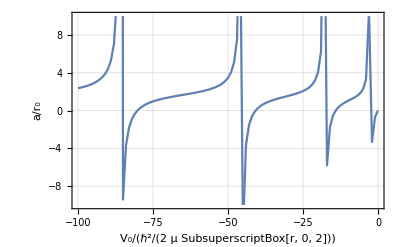

```mathematica
ListPlot[Transpose[a2r2][[1]],Frame->True,LabelStyle->Medium,GridLines->Automatic,FrameLabel->{"V_0/(ℏ^2/(2  μ SubsuperscriptBox[r, 0, 2]))","a/r_0"},Joined->True,PlotRange->{-10,10}]
```

Let’s test that this gives the right answer for the square-well.  The exact answer is

```mathematica
Ksqrwell[V0_,Ε_]:=Module[{γ,α,K,k},
α=√(V0+Ε);
γ=D[SphericalBesselJ[0,α r],r]/SphericalBesselJ[0,α r]/.r->1;
k=√Ε;
K=(D[SphericalBesselJ[0,k r],r]-γ SphericalBesselJ[0,k ])/(D[SphericalBesselY[0,k r],r]-γ SphericalBesselY[0,k ])/.r->1;
N[K]
]
```

```mathematica
Vsqr[V0_,r_]:=Piecewise[{{-V0,r<1},{0,r≥1}}]
```

```mathematica
Clear[se,sp,ce,cp]
```

```mathematica
se[l_,k_,r_]:=√(k/π)r SphericalBesselJ[l,k r]
ce[l_,k_,r_]:=√(k/π)r SphericalBesselY[l,k r]
```

```mathematica
sp[l_,k_,r_]=Simplify[D[se[l,k,r],r]];

cp[l_,k_,r_]=Simplify[D[ce[l,k,r],r]];
```

```mathematica
CalcCotanDeltaSqr[v0_?NumberQ,r0_?NumberQ,ksqr_?NumberQ,rmax_?NumberQ]:=
Module[{vlocal,CotanDelta,sol,k,u1,u2,r1,r2,K,u,r,Y},
r1=0.95 rmax;
r2=0.99rmax;
vlocal=v0;
k=√ksqr;
sol=NDSolve[{-u''[r]+Vsqr[vlocal,r]u[r]==ksqr u[r],u[0]==0,u'[0]==1},u,{r,0,rmax},Method->"ExplicitRungeKutta"];
u1=u[r1]/.sol[[1]];
u2=u[r2]/.sol[[1]];
CotanDelta=(-u2 Cos[k r1]+u1 Cos[k r2])/(u2 Sin[k r1]-u1 Sin[k r2]);
Y=D[Log[u[r]],r]/.sol[[1]]/.r->rmax;
K=(sp[0,k,rmax]-Y se[0,k,rmax])/(cp[0,k,rmax] - Y ce[0,k,rmax]);
Return[{CotanDelta,K}]
]
```

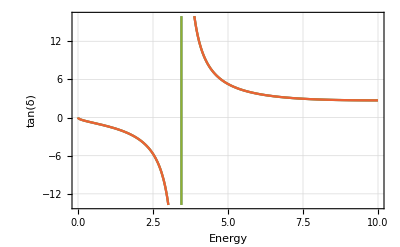

```mathematica
Plot[{(CalcCotanDeltaSqr[10.,1.,Ε,2][[1]])^-1,,CalcCotanDeltaSqr[10.,1.,Ε,2][[2]],Ksqrwell[10,Ε]},{Ε,0,10},Frame->True,GridLines->Automatic,LabelStyle->Large,FrameLabel->{"Energy","tan(δ)"}]
```

Ok, this looks good!  All three answers agree with each other, and the results for tan(δ) look reasonable.